# Qubism Wolfram Mathematica supporting materials for arXiv:1112.3560

## Introduction

The current version is on http://qubism.wikidot.com.
Distributed under the Creative Commons Attriburtion 3.0 Licence.
Authored by Piotr Migdał, ICFO-The Institute of Photonic Sciences, Castelldefels (Barcelona).
Version 0.2 (21 Dec 2011)
- some functions changed
- added some functions for ploting
- added examples (there were none)
previous version: 0.1 (20 Dec 2011)

## Generating and manipulating quantum states

### Function definitions

```mathematica
(* |ψ⟩ ↦ |ψ⟩⊗|ψ⟩⊗...⊗|ψ⟩ *)
VectorTensorPower[vec_,n_]:=
Module[{tmp},
tmp=vec;
Do[tmp=Flatten[Outer[Times,vec,tmp]],{n-1}];
tmp
];
(* A ↦ A ⊗ A ⊗...⊗ A *)
MatrixTensorPower[mat_,n_]:=
Module[{tmp},
tmp=mat;
Do[tmp=KroneckerProduct[mat,tmp],{n-1}];
tmp
];
(* Shifts a qudit state, i.e., k-th particle now becomes (k+1)-th and nth - first. *)
QuditShift[wf_,d_:2]:=
Flatten[Transpose[Partition[wf,d]]];
```

```mathematica
(* Transforms a vector into a density matrix *)
VectorToDensityMatrix[vec_]:=KroneckerProduct[vec,Conjugate[vec]];
```

```mathematica
(* Hamiltonian H = cos(α) ∑Subscript[(σ^z), i] Subscript[(σ^z), i+1]-sin(α)∑Subscript[(σ^x), i],
by default with the periodic boundary conditions *)
AntiFerroHam[n_,alpha_:0,bcond_:AntiFerroEnergyCyc]:=
Module[{posdiag,valdiag,posoff,valoff},
posdiag=Table[{i+1,i+1},{i,0,2^n-1}];
valdiag=Cos[alpha] Table[bcond[IntegerToSpin[i,n]],{i,0,2^n-1}];
posoff=Flatten[Table[{i+1,FromDigits[MapAt[Flip,PadLeft[IntegerDigits[i,2],n],j],2]+1},{i,0,2^n-1},{j,1,n}],1];
valoff=-Sin[alpha] Table[1,{i,1,n 2^n}];
SparseArray[Join[posdiag,posoff]->Join[valdiag,valoff]]+SparseArray[{{i_, i_}->n}, {2^n,2^n}]
];
(* Functions depending on open or periodic boundary conditions *)
AntiFerroEnergy[li_]:=Total[Map[(#[[1]]*#[[2]])&,Partition[li,2,1]]];
AntiFerroEnergyCyc[li_]:=Total[Map[(#[[1]]*#[[2]])&,Partition[li,2,1]]]+li[[1]]*li[[-1]];
(* Auxiliary *)
IntegerToSpin[int_,n_]:=(-2PadLeft[IntegerDigits[int,2],n]+1);
Flip[x_]:=1-x;
```

```mathematica
(* Dicke state *)
DickeState[nparticles_,kexcited_]:=
Binomial[nparticles,kexcited]^(-1/2) Table[
If[
Total[IntegerDigits[i,2]]==kexcited,
1,
0],
{i,0,2^nparticles-1}];
```

```mathematica
(* AKLT state *)
HaldaneState[n_]:=Module[{tmp},
tmp=Table[HorNot[IntegerDigits[i,3,n]],{i,0,3^n-1}];
tmp/√Total[tmp^2]];
(* Using auxiliary *)
HorNot[li_]:=If[MemberQ[Differences[Select[li,(#==0||#==2)&]],0]||(Count[li,0]≠Count[li,2]),0,1];
```

```mathematica
PauliExpectedValueWf[wavefunction_,paulilist_]:=
Module[{matlist},
matlist=Map[SparseArray,PauliMatrix[paulilist]];
Conjugate[wavefunction].((KroneckerProduct@@matlist).wavefunction)
];
PauliExpectedValueWfTable[wavefunction_]:=
Module[{qubits},
qubits=Log[2,Length[wavefunction]];
Table[
PauliExpectedValueWf[wavefunction,(2 IntegerDigits[i,2,qubits])+(IntegerDigits[j,2,qubits])],
{i,0,2^qubits-1},{j,0,2^qubits-1}]
];
```

```mathematica
PauliExpectedValueWfTable[wavefunction_,axis_:{1,2}]:=
Module[{qubits},
qubits=Log[2,Length[wavefunction]];
Table[
PauliExpectedValueWf[wavefunction,
Map[CordRot,(axis[[1]] IntegerDigits[x,2,qubits])+(axis[[2]] IntegerDigits[y,2,qubits])]
],
{y,0,2^qubits-1},{x,0,2^qubits-1}]];
CordRot:=If[#≥ 4,6-#,#]&;
```

### Examples

```mathematica
VectorTensorPower[{Cos[α],Sin[α]},2]
```

{Cos[α]^2,Cos[α] Sin[α],Cos[α] Sin[α],Sin[α]^2}

```mathematica
DickeState[4,2]
```

{0,0,0,1/(√6),0,1/(√6),1/(√6),0,0,1/(√6),1/(√6),0,1/(√6),0,0,0}

```mathematica
(* qubit singlet pairs 1-2 and 3-4 *)
VectorTensorPower[{0,1/(√2),-1/(√2),0},2]
```

{0,0,0,0,0,1/2,-1/2,0,0,-1/2,1/2,0,0,0,0,0}

```mathematica
(* qubit singlet pairs 2-3 and 4-1 *)
QuditShift[VectorTensorPower[{0,1/(√2),-1/(√2),0},2]]
```

{0,0,0,-1/2,0,1/2,0,0,0,0,1/2,0,-1/2,0,0,0}

```mathematica
VectorToDensityMatrix[{1/(√2),1/2,I/2}]//MatrixForm
```

(1/2 | 1/(2 √2) | -ⅈ/(2 √2)
1/(2 √2) | 1/4 | -ⅈ/4
ⅈ/(2 √2) | ⅈ/4 | 1/4)

```mathematica
HaldaneState[3]
```

{0,0,0,0,0,1/(√7),0,1/(√7),0,0,0,1/(√7),0,1/(√7),0,1/(√7),0,0,0,1/(√7),0,1/(√7),0,0,0,0,0}

```mathematica
(* ground state of ITF hamiltonian with ArcTan[Γ]=0.3 for 4 particles with periodic boundary conditions *)
Eigenvectors[
AntiFerroHam[4,0.3],
-1][[1]]
```

{0.00853198,-0.055846,-0.055846,0.0168578,-0.055846,0.697771,0.0168578,-0.055846,-0.055846,0.0168578,0.697771,-0.055846,0.0168578,-0.055846,-0.055846,0.00853198}

```mathematica
(* ground state of ITF hamiltonian with ArcTan[Γ]=0.3 for 4 particles with periodic boundary conditions *)
Eigenvectors[
AntiFerroHam[4,0.3],
-1][[1]]
```

{0.00853198,-0.055846,-0.055846,0.0168578,-0.055846,0.697771,0.0168578,-0.055846,-0.055846,0.0168578,0.697771,-0.055846,0.0168578,-0.055846,-0.055846,0.00853198}

```mathematica
(* ... and with open boundary conditions *)
Eigenvectors[
AntiFerroHam[4,0.3,AntiFerroEnergy],
-1][[1]]
```

{0.0169521,-0.0575604,-0.111033,0.0251161,-0.111033,0.68224,0.0484486,-0.0575604,-0.0575604,0.0484486,0.68224,-0.111033,0.0251161,-0.111033,-0.0575604,0.0169521}

## Ploting

### Function definitions

```mathematica
(* A function changing index into 2 indexes for X and Y position, respectively
i-index,
n - total number of particles; need to be even,
d - dimension (i.e. 2 for qubits),
rot - 0 for standard cordinates, -1 for ferro-antiferro *)
IndexTo2DimCord[i_,n_,d_:2,rot_:0]:=
Module[{bin},
bin=PadLeft[IntegerDigits[i,d],n];
{
FromDigits[Take[bin,{1,-1,2}],d],
FromDigits[Mod[Take[bin,{2,-1,2}]+rot Take[bin,{1,-1,2}],d],d]
}
];
```

```mathematica
(* Square plots,
d=2 for qubits, d=3 for qutrits,
rot=0 for standard mapping, rot=-1 for a modifed scheme (i.e. ferro-antiferro scheme for qubits) *)
QubismSquare[wf_,d_:2,rot_:0,pixsize_:4,scaling_:1.,colors_:ComplexColors]:=
Module[{n,maxabs},
n=Log[d,Length[wf]];
maxabs=Max[Abs[wf]]/scaling;
ArrayPlot[
SparseArray[Table[IndexTo2DimCord[i,n,d,rot]+1,{i,0,d^n-1}]->(wf/maxabs)],
ColorFunction->colors,ColorFunctionScaling->False,PixelConstrained->{pixsize,pixsize}]
];
```

```mathematica
(* A color scheme for unit complex disk*)
ComplexColors:=Hue[(Arg[#])/(2π),Abs[#],1-Abs[#]/4]&
```

```mathematica
BinaryTicks[logn_,step_:0,offset_:0]:=
Table[{i+1+offset,StringJoin[IntegerDigits[i,2,logn]/.{0->"0",1->"1"}]},{i,0,2^logn-1,2^step}];
```

```mathematica
(* Ploting Pauli correlations *)
QubismPauli[wf_,ticksnolog_:{4,2},axes_:{1,2}]:=
Module[{n},
n=Log[2,Length[wf]];
ArrayPlot[Chop[PauliExpectedValueWfTable[wf,axes]],Mesh->{{0,{2^(n-2),Dashed},2^(n-1),{3 2^(n-2),Dashed},2^n},{0,{2^(n-2),Dashed},2^(n-1),{3 2^(n-2),Dashed},2^n}},Frame->True,FrameStyle->Directive[White],FrameTicksStyle->Directive[Black,12],FrameTicks->{{BinaryTicks[n,n-ticksnolog[[1]]],None},{BinaryTicks[n,n-ticksnolog[[2]]],None}},ColorFunctionScaling->False,ColorFunction->ComplexColors,DataReversed->True]
];
```

```mathematica
(* Triangular ploting schemes *)
QubismTriangular[wf_,colorfun_,nextcordfunct_,scaling_:1.]:=
Module[{len,qubits,colors,triangles,edges,maxabs,line},
len=Length[wf];
qubits=Log[2,len];
maxabs=Max[Abs[wf]]/scaling;
colors=Map[colorfun,(wf/maxabs)];
edges=Map[EdgeForm[{Thickness[0.001],#}]&,colors];
triangles=Table[
Polygon[
Fold[nextcordfunct,{{-1,0},{0,1},{1,0}},IntegerDigits[i-1,2,qubits]]
],
{i,1,len}];
line={Black,Thickness[0.002],Line[{{-1,0},{0,1},{1,0},{-1,0}}]};
Graphics[Flatten[{Transpose[{colors,edges,triangles}],line}],PlotRange->{{-1,1},{-0.05,1}},AspectRatio->1/2]
];
(* nextcordfunct should take one of the following functions *)
TriangleNextCord[{a_,b_,c_},bit_]:=
If[bit==0,
{b,(a+c)/2,a},
{c,(a+c)/2,b}
];
TriangleNextCordRefl[{a_,b_,c_},bit_]:=
If[bit==0,
{a,(a+c)/2,b},
{b,(a+c)/2,c}
];
```

```mathematica
QubismSchemeTriangular[depth_,nextcordfunct_,lims_:False]:=
Module[{triangles,bits,vertcords,special},
triangles=Table[
bits=IntegerDigits[i-1,2,depth];
vertcords=Fold[nextcordfunct,{{-1,0},{0,1},{1,0}},bits];
{Line[vertcords[[{1,2,3,1}]]],
Text[Style[StringJoin[Map[ToString,bits]],FontSize->4(8-depth)],(vertcords[[1]]+1.5vertcords[[2]]+vertcords[[3]])/3.5]},
{i,1,2^depth}];
special=If[lims,
{
PointSize[Large],
Blue,
Point[Mean[Fold[nextcordfunct,{{-1.,0.},{0.,1.},{1.,0.}},Table[0,{128}]]]],
Point[Mean[Fold[nextcordfunct,{{-1.,0.},{0.,1.},{1.,0.}},Table[Mod[i,2],{i,128}]]]],
Point[Mean[Fold[nextcordfunct,{{-1.,0.},{0.,1.},{1.,0.}},Table[1,{128}]]]],Point[Mean[Fold[nextcordfunct,{{-1.,0.},{0.,1.},{1.,0.}},Table[Mod[i+1,2],{i,128}]]]]
},{}];
Graphics[
Flatten[{Thin,triangles,special}],
PlotRange->{{-1.05,1.05},{-0.05,1.05}},AspectRatio->1/2]
];
```

### Examples

#### Square plots - standard

The most standard scheme from the paper. 
rot=0

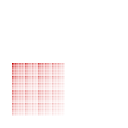

```mathematica
(* A separable state *)
QubismSquare[
VectorTensorPower[{Cos[0.6],Sin[0.6]},12],
2,0,2]
```

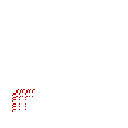
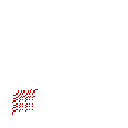
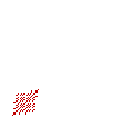
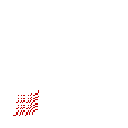
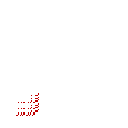
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* All Dicke states for n=10 *)
Table[
QubismSquare[
DickeState[10,k],
2,0,4],
{k,0,10}]
```

```mathematica
(* Products of 4 singlet pairs: 1-2, 3-4, 5-6 and 7-8
and 2-3, 4-5, 6-7, 8-1 *)
{QubismSquare[
VectorTensorPower[{0,1/(√2.),-1/(√2.),0},5],
2,0,4],
QubismSquare[
QuditShift[VectorTensorPower[{0,1/(√2.),-1/(√2.),0},5]],
2,0,4]}
```

{-Graphics-,-Graphics-}

```mathematica
(* Ground state of the Heisenberg Hamiltonian; copied form a C++ program *)
heis6ground={0,0,0,0,0,0,0,-0.0629206215187,0,0,0,0.207812695863,0,-0.207812695863,0.0629206215187,0,0,0,0,-0.207812695863,0,0.478546013245,-0.207812695863,0,0,-0.207812695863,0.207812695863,0,-0.0629206215187,0,0,0,0,0,0,0.0629206215187,0,-0.207812695863,0.207812695863,0,0,0.207812695863,-0.478546013245,0,0.207812695863,0,0,0,0,-0.0629206215187,0.207812695863,0,-0.207812695863,0,0,0,0.0629206215187,0,0,0,0,0,0,0};
QubismSquare[
heis6ground,
2,0,16]
```

-Graphics-

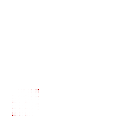
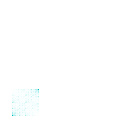
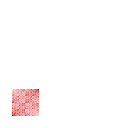
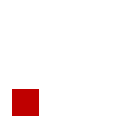
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Gound states for ITF Hamiltonian for different α=ArcTan[Γ] *)
Table[
QubismSquare[
Eigenvectors[
AntiFerroHam[10,α],
-1][[1]],
2,0,4],
{α,0.,π/2.,π/8.}]
```

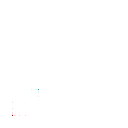
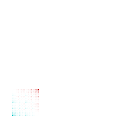
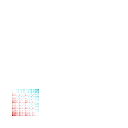
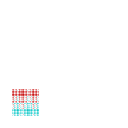
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* ...and the first excited *)
Table[
QubismSquare[
Eigenvectors[
AntiFerroHam[10,α],
-2][[1]],
2,0,4],
{α,0.,π/2.,π/8.}]
```

```mathematica
(* AKLT/Haldane state *)
QubismSquare[
HaldaneState[8],
3,0,4]
```

-Graphics-

#### Square plots - ferro-antiferro

The most standard scheme from the paper. 
rot ≠ 0 (for qubits it is equivalent to rot=1 )

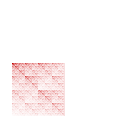

```mathematica
(* A separable state *)
QubismSquare[
VectorTensorPower[{Cos[0.6],Sin[0.6]},12],
2,1,2]
```

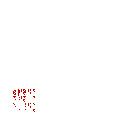
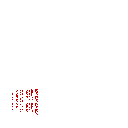
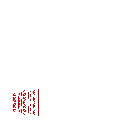
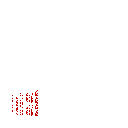
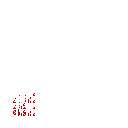
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* All Dicke states for n=10 *)
Table[
QubismSquare[
DickeState[10,k],
2,1,4],
{k,0,10}]
```

```mathematica
(* Products of 4 singlet pairs: 1-2, 3-4, 5-6 and 7-8
and 2-3, 4-5, 6-7, 8-1 *)
{QubismSquare[
VectorTensorPower[{0,1/(√2.),-1/(√2.),0},5],
2,1,4],
QubismSquare[
QuditShift[VectorTensorPower[{0,1/(√2.),-1/(√2.),0},5]],
2,1,4]}
```

{-Graphics-,-Graphics-}

```mathematica
(* Ground state of the Heisenberg Hamiltonian; copied form a C++ program *)
heis6ground={0,0,0,0,0,0,0,-0.0629206215187,0,0,0,0.207812695863,0,-0.207812695863,0.0629206215187,0,0,0,0,-0.207812695863,0,0.478546013245,-0.207812695863,0,0,-0.207812695863,0.207812695863,0,-0.0629206215187,0,0,0,0,0,0,0.0629206215187,0,-0.207812695863,0.207812695863,0,0,0.207812695863,-0.478546013245,0,0.207812695863,0,0,0,0,-0.0629206215187,0.207812695863,0,-0.207812695863,0,0,0,0.0629206215187,0,0,0,0,0,0,0};
QubismSquare[
heis6ground,
2,1,16]
```

-Graphics-

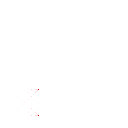
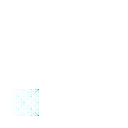
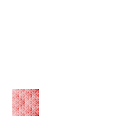
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* Gound states for ITF Hamiltonian for different α=ArcTan[Γ] *)
Table[
QubismSquare[
Eigenvectors[
AntiFerroHam[10,α],
-1][[1]],
2,1,4],
{α,0.,π/2.,π/8.}]
```

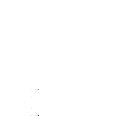
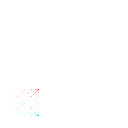
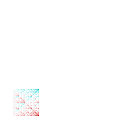
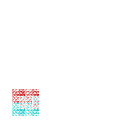
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* ...and the first excited *)
Table[
QubismSquare[
Eigenvectors[
AntiFerroHam[10,α],
-2][[1]],
2,1,4],
{α,0.,π/2.,π/8.}]
```

```mathematica
(* AKLT/Haldane state *)
QubismSquare[
HaldaneState[8],
3,-1,4]
```

-Graphics-

```mathematica
QubismSquare[
HaldaneState[8],
3,+1,4]
```

-Graphics-

#### Triangular plots- standard

How does it work - 3 subsequent iterations.
The 3rd plot shows limits for ferromagnetic (0000... and 1111...) and antiferromagnetic (0101... and 1010...) states.

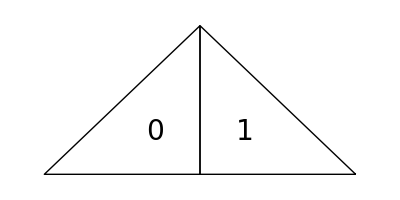

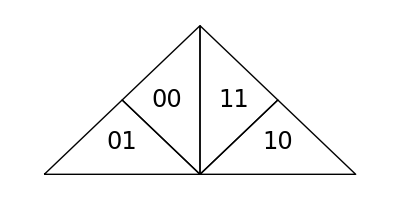

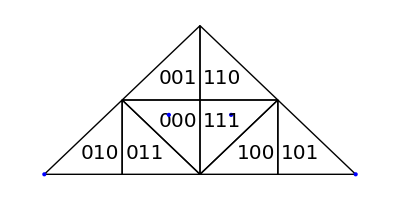

```mathematica
QubismSchemeTriangular[1,TriangleNextCord]
QubismSchemeTriangular[2,TriangleNextCord]
QubismSchemeTriangular[3,TriangleNextCord,True]
```

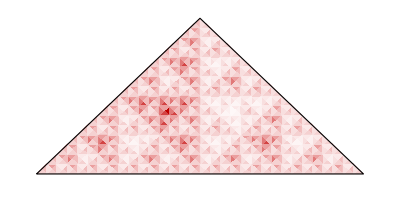

```mathematica
(* A separable state *)
QubismTriangular[
VectorTensorPower[{Cos[0.6],Sin[0.6]},10],
ComplexColors,TriangleNextCord]
```

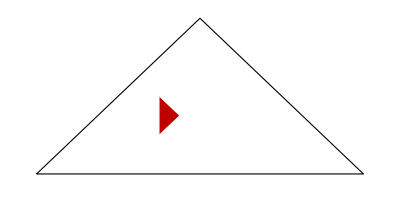
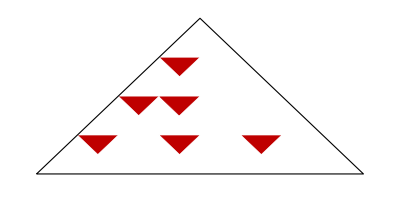
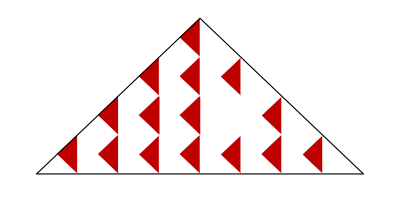
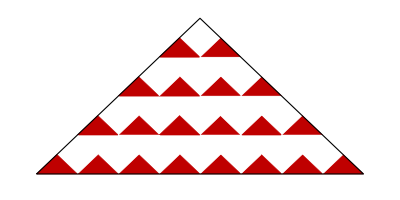
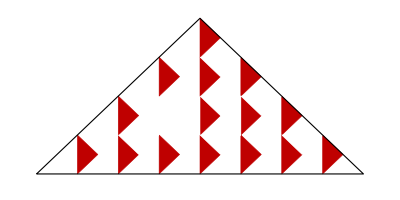
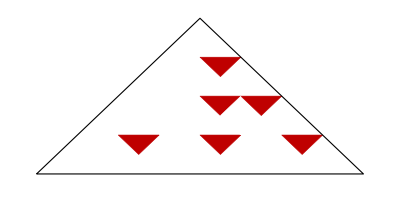
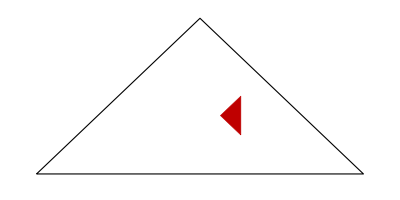

```mathematica
(* All Dicke states for n=6 *)
Table[
QubismTriangular[
DickeState[6,k],
ComplexColors,TriangleNextCord],
{k,0,6}]
```

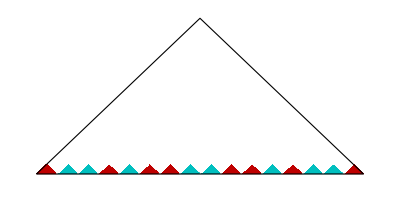
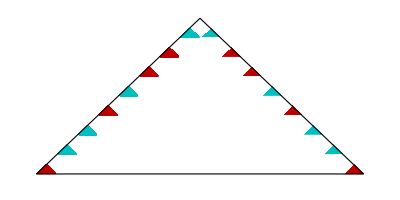

```mathematica
(* Products of 4 singlet pairs: 1-2, 3-4, 5-6 and 7-8
and 2-3, 4-5, 6-7, 8-1 *)
{QubismTriangular[
VectorTensorPower[{0,1/(√2.),-1/(√2.),0},4],
ComplexColors,TriangleNextCord],
QubismTriangular[
QuditShift[VectorTensorPower[{0,1/(√2.),-1/(√2.),0},4]],
ComplexColors,TriangleNextCord]}
```

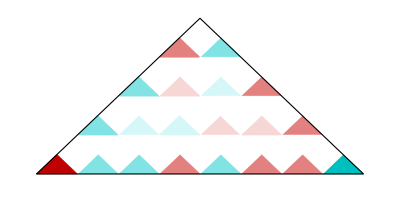

```mathematica
(* Ground state of the Heisenberg Hamiltonian; copied form a C++ program *)
heis6ground={0,0,0,0,0,0,0,-0.0629206215187,0,0,0,0.207812695863,0,-0.207812695863,0.0629206215187,0,0,0,0,-0.207812695863,0,0.478546013245,-0.207812695863,0,0,-0.207812695863,0.207812695863,0,-0.0629206215187,0,0,0,0,0,0,0.0629206215187,0,-0.207812695863,0.207812695863,0,0,0.207812695863,-0.478546013245,0,0.207812695863,0,0,0,0,-0.0629206215187,0.207812695863,0,-0.207812695863,0,0,0,0.0629206215187,0,0,0,0,0,0,0};
QubismTriangular[
heis6ground,
ComplexColors,TriangleNextCord]
```

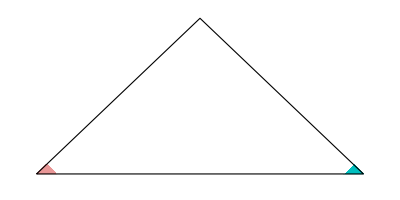
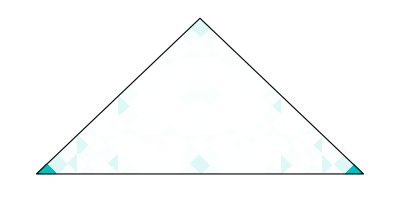
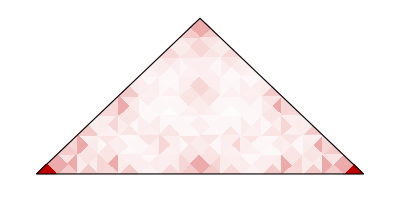
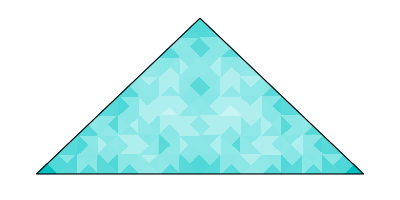
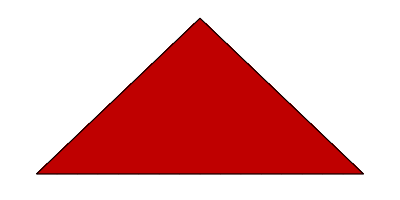

```mathematica
(* Gound states for ITF Hamiltonian for different α=ArcTan[Γ] *)
Table[
QubismTriangular[
Eigenvectors[
AntiFerroHam[8,α],
-1][[1]],
ComplexColors,TriangleNextCord],
{α,0.,π/2.,π/8.}]
```

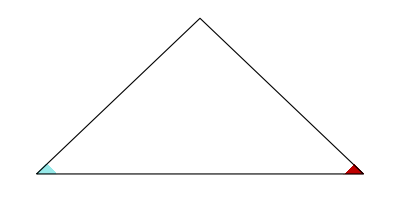
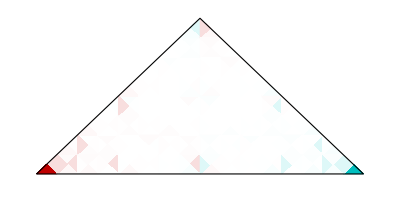
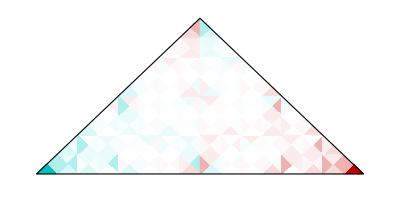
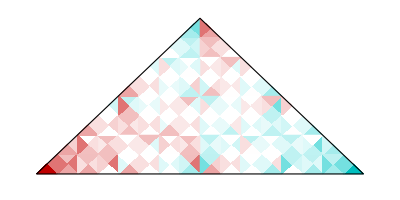
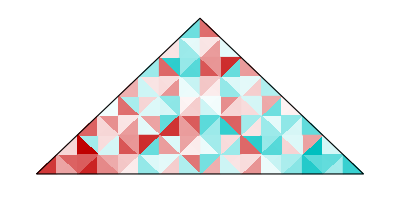

```mathematica
Table[
QubismTriangular[
Eigenvectors[
AntiFerroHam[8,α],
-2][[1]],
ComplexColors,TriangleNextCord],
{α,0.,π/2.,π/8.}]
```

#### Triangular plots - reflected

How does it work - 3 subsequent iterations.
The 3rd plot shows limits for ferromagnetic (0000... and 1111...) and antiferromagnetic (0101... and 1010...) states.
Note that the limitis are interchanged FM<->AFM (relating it to the standard triangular scheme).

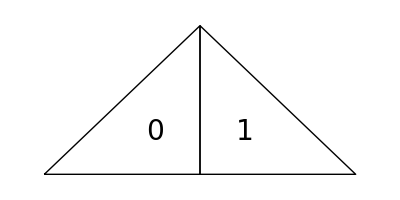

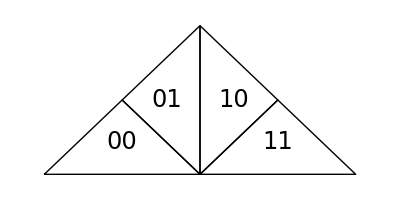

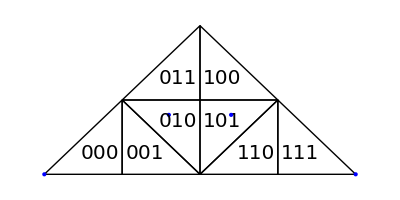

```mathematica
QubismSchemeTriangular[1,TriangleNextCordRefl]
QubismSchemeTriangular[2,TriangleNextCordRefl]
QubismSchemeTriangular[3,TriangleNextCordRefl,True]
```

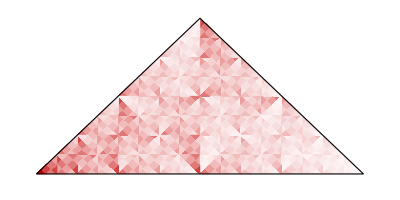

```mathematica
(* A separable state *)
QubismTriangular[
VectorTensorPower[{Cos[0.6],Sin[0.6]},10],
ComplexColors,TriangleNextCordRefl]
```

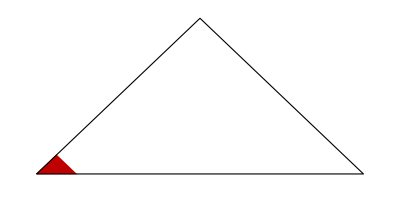
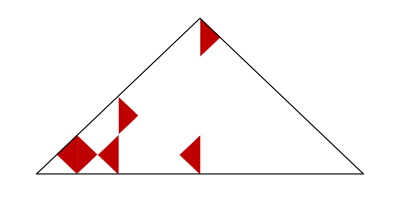
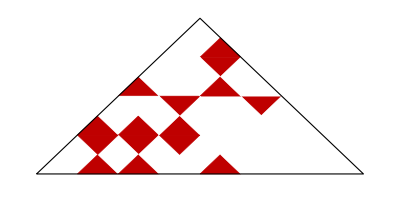
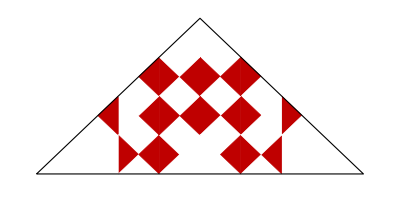
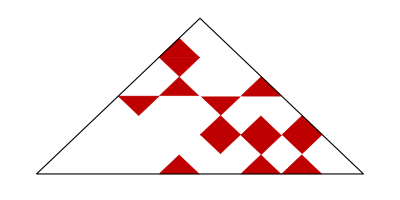
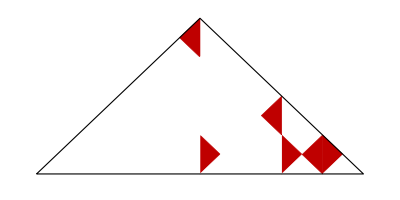
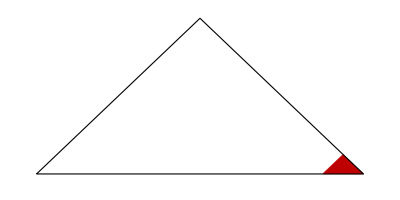

```mathematica
(* All Dicke states for n=6 *)
Table[
QubismTriangular[
DickeState[6,k],
ComplexColors,TriangleNextCordRefl],
{k,0,6}]
```

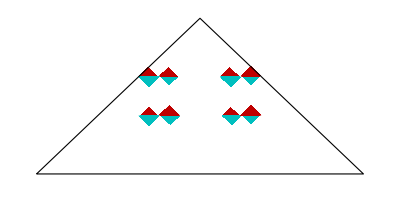
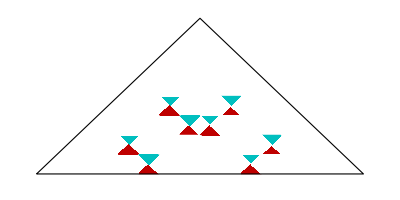

```mathematica
(* Products of 4 singlet pairs: 1-2, 3-4, 5-6 and 7-8
and 2-3, 4-5, 6-7, 8-1 *)
{QubismTriangular[
VectorTensorPower[{0,1/(√2.),-1/(√2.),0},4],
ComplexColors,TriangleNextCordRefl],
QubismTriangular[
QuditShift[VectorTensorPower[{0,1/(√2.),-1/(√2.),0},4]],
ComplexColors,TriangleNextCordRefl]}
```

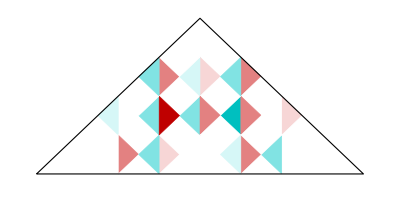

```mathematica
(* Ground state of the Heisenberg Hamiltonian; copied form a C++ program *)
heis6ground={0,0,0,0,0,0,0,-0.0629206215187,0,0,0,0.207812695863,0,-0.207812695863,0.0629206215187,0,0,0,0,-0.207812695863,0,0.478546013245,-0.207812695863,0,0,-0.207812695863,0.207812695863,0,-0.0629206215187,0,0,0,0,0,0,0.0629206215187,0,-0.207812695863,0.207812695863,0,0,0.207812695863,-0.478546013245,0,0.207812695863,0,0,0,0,-0.0629206215187,0.207812695863,0,-0.207812695863,0,0,0,0.0629206215187,0,0,0,0,0,0,0};
QubismTriangular[
heis6,
ComplexColors,TriangleNextCordRefl]
```

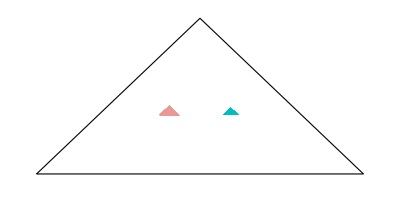
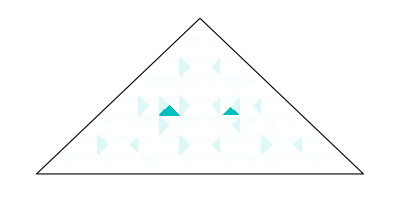
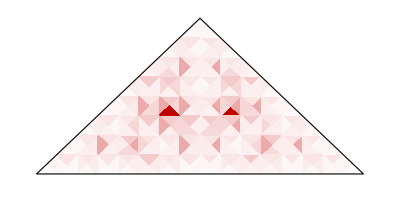
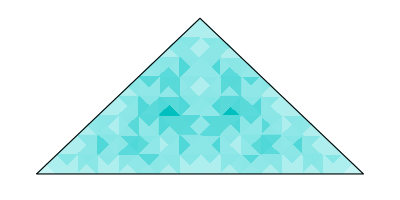
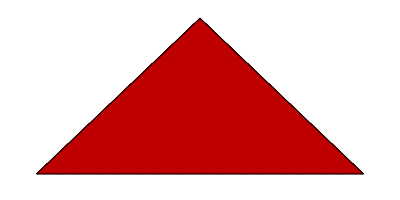

```mathematica
(* Gound states for ITF Hamiltonian for different α=ArcTan[Γ] *)
Table[
QubismTriangular[
Eigenvectors[
AntiFerroHam[8,α],
-1][[1]],
ComplexColors,TriangleNextCordRefl],
{α,0.,π/2.,π/8.}]
```

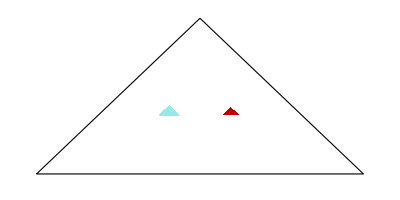
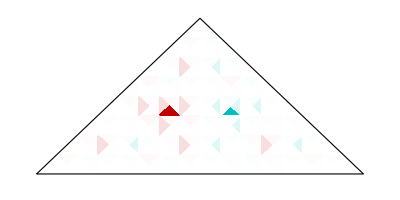
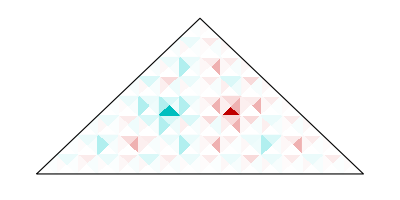
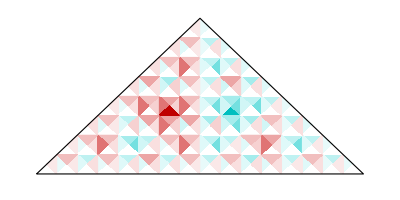
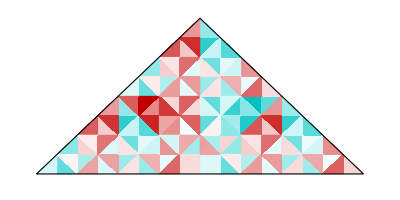

```mathematica
Table[
QubismTriangular[
Eigenvectors[
AntiFerroHam[8,α],
-2][[1]],
ComplexColors,TriangleNextCordRefl],
{α,0.,π/2.,π/8.}]
```

#### Pauli plots

What is that - see arXiv:1112.3560v1, Fig. 22.

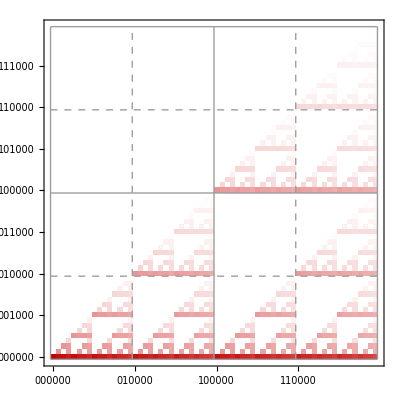

```mathematica
(* A separable state *)
QubismPauli[
VectorTensorPower[{Cos[0.6],Sin[0.6]},6]
]
```

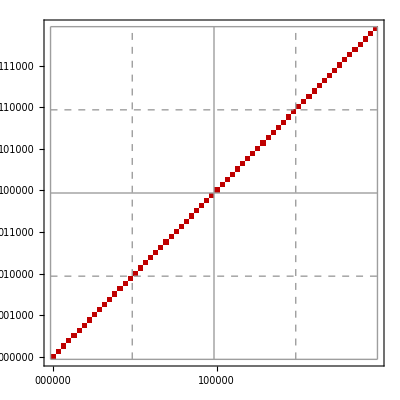
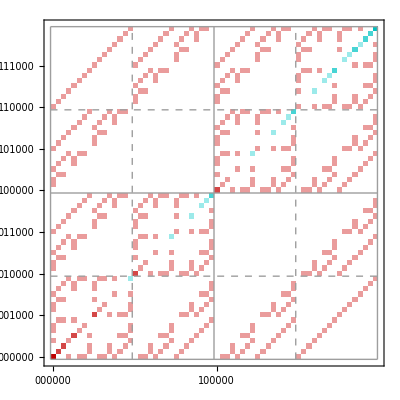
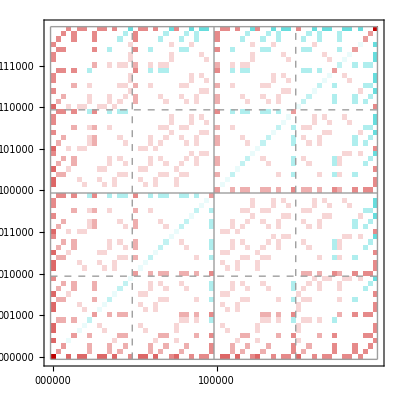
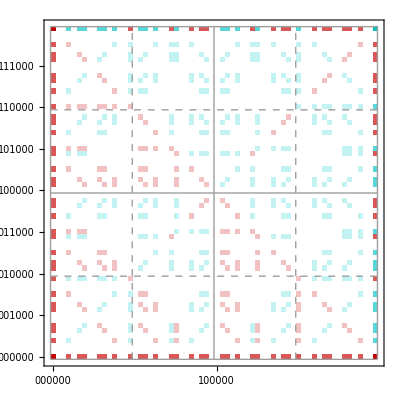
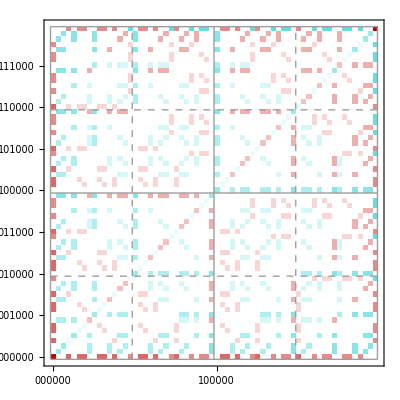
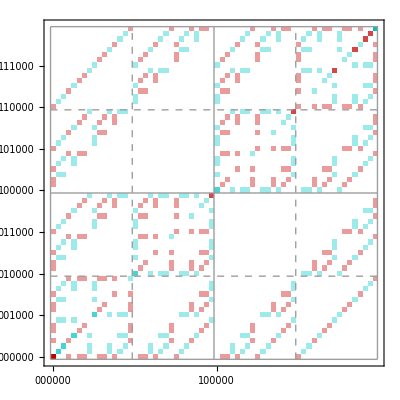
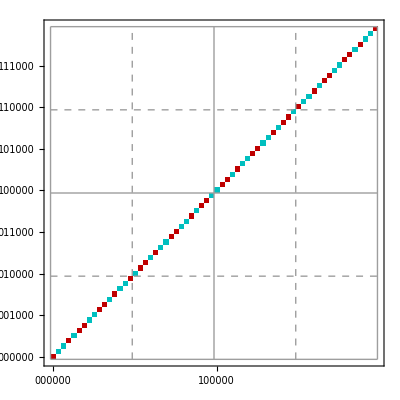

```mathematica
(* All Dicke states for n=6 *)
Table[
QubismPauli[DickeState[6,k],{3,1}],
{k,0,6}]
```

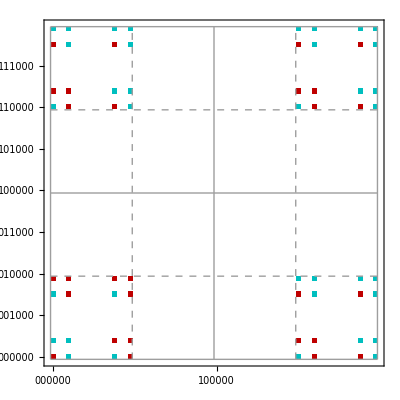
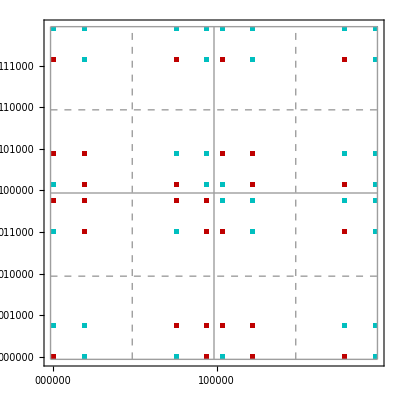

```mathematica
(* Products of 4 singlet pairs: 1-2, 3-4, 5-6 and 7-8
and 2-3, 4-5, 6-7, 8-1 *)
{QubismPauli[
VectorTensorPower[{0,1/(√2.),-1/(√2.),0},3],{3,1}
],
QubismPauli[
QuditShift[VectorTensorPower[{0,1/(√2.),-1/(√2.),0},3]],{3,1}
]}
```

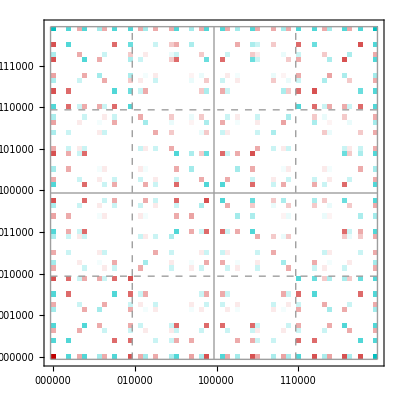

```mathematica
(* Ground state of the Heisenberg Hamiltonian; copied form a C++ program *)
heis6ground={0,0,0,0,0,0,0,-0.0629206215187,0,0,0,0.207812695863,0,-0.207812695863,0.0629206215187,0,0,0,0,-0.207812695863,0,0.478546013245,-0.207812695863,0,0,-0.207812695863,0.207812695863,0,-0.0629206215187,0,0,0,0,0,0,0.0629206215187,0,-0.207812695863,0.207812695863,0,0,0.207812695863,-0.478546013245,0,0.207812695863,0,0,0,0,-0.0629206215187,0.207812695863,0,-0.207812695863,0,0,0,0.0629206215187,0,0,0,0,0,0,0};
QubismPauli[heis6ground]
```

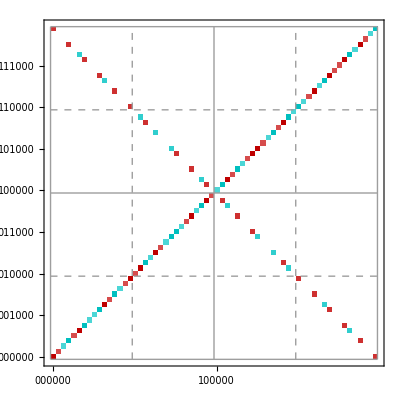
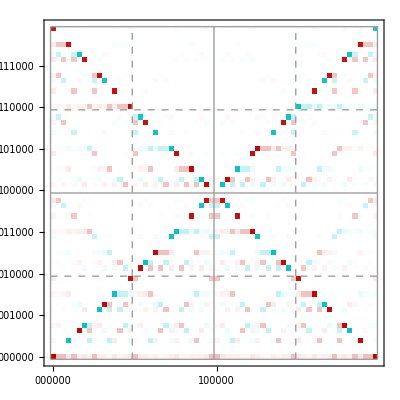
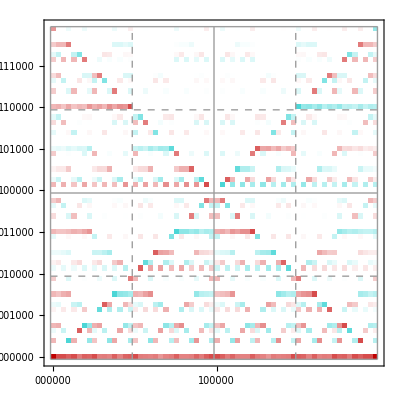
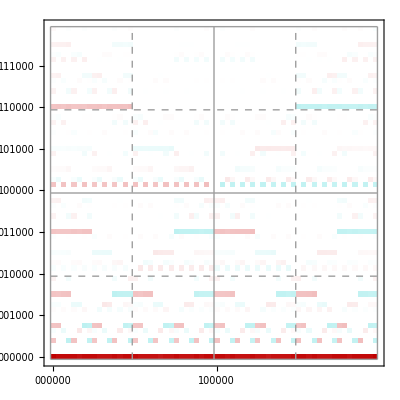
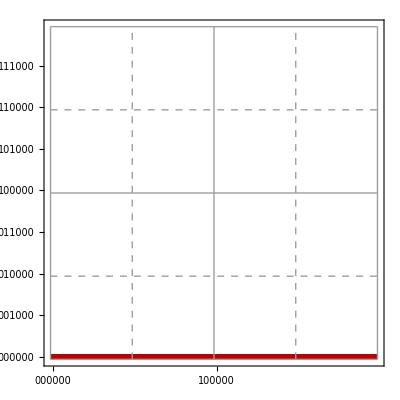

```mathematica
(* Gound states for ITF Hamiltonian for different α=ArcTan[Γ] *)
Table[
QubismPauli[
Evaluate[Eigenvectors[
AntiFerroHam[6,α],
-1][[1]]],
{3,1},{1,2}],
{α,0.,π/2.,π/8.}]
```

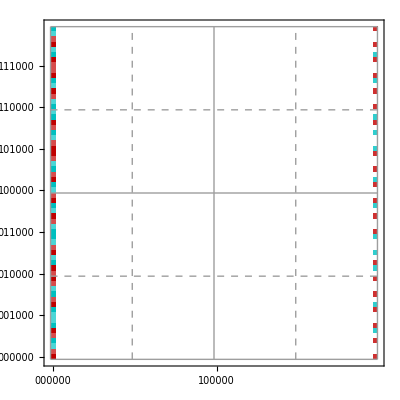
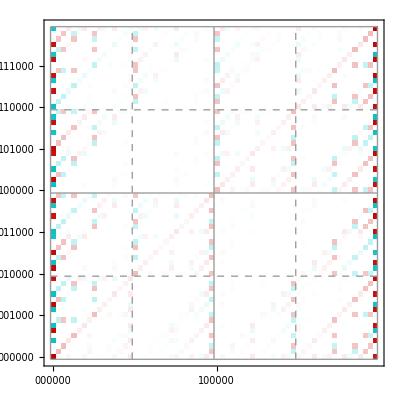
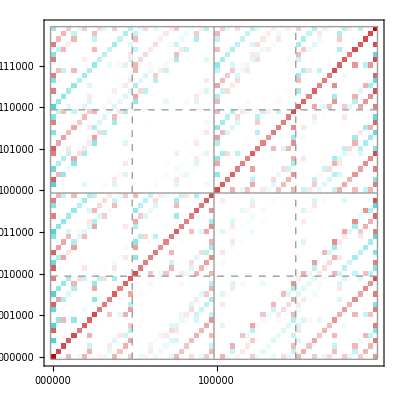
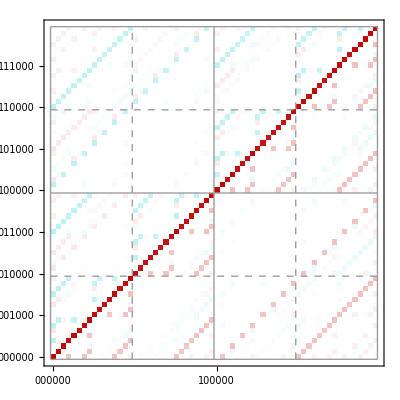
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* The same stuff but for YZ axes *)
Table[
QubismPauli[
Evaluate[Eigenvectors[
AntiFerroHam[6,α],
-1][[1]]],
{3,1},{2,3}],
{α,0.,π/2.,π/8.}]
```

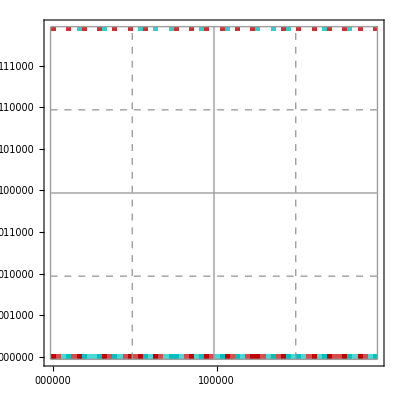
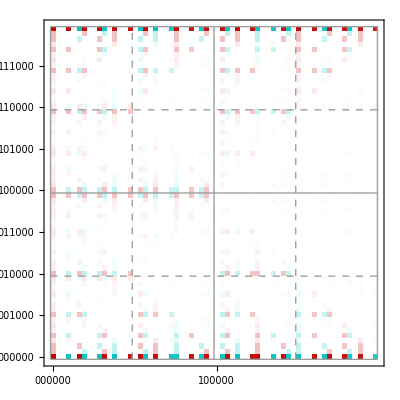
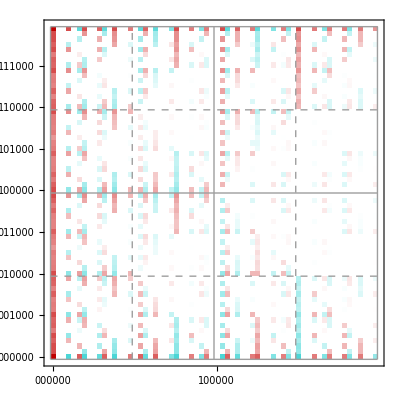
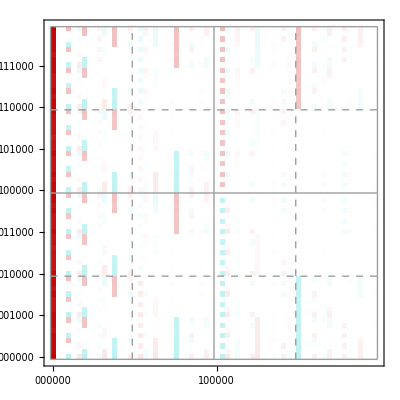
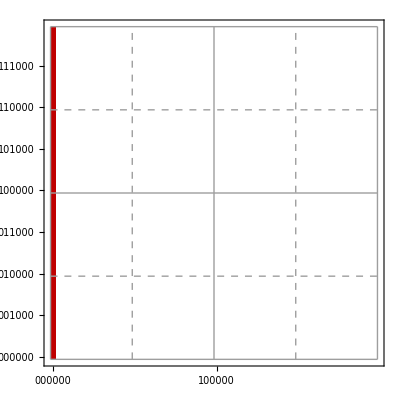

```mathematica
(* The same stuff but for ZX axes *)
Table[
QubismPauli[
Evaluate[Eigenvectors[
AntiFerroHam[6,α],
-1][[1]]],
{3,1},{3,1}],
{α,0.,π/2.,π/8.}]
```

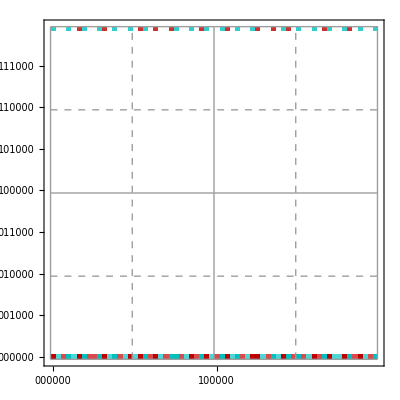
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* And ZX axes for the first excited state *)
Table[
QubismPauli[
Eigenvectors[
AntiFerroHam[6,α],
-2][[1]],
{3,1},{3,1}],
{α,0.,π/2.,π/8.}]
```

## Analysis of self-similiarity

coming soon (er or later)